```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
$N = 3;
```

```mathematica
mats = (# - 1/($N)Tr[#]*IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[1, $N], 10000];
```

```mathematica
data = Import["../../runs/Trials/N3K9/81218541.dat"];
```

```mathematica
changeNK[3, 9];
```

```mathematica
cmatdata = cMatOne/@data;
```

```mathematica
diag = Flatten@Table[cmatdata[[10000;;,2;;, a, a]]/(√(($N-1)/($N)))//Chop, {a, 1, $N}];
```

```mathematica
offdiag = Flatten@Table[(ReIm@cmatdata[[10000;;, 2;;, i, j]])/(1/(√2)), {i, 1, $N}, {j, i+1, $N}];
```

```mathematica
σ = StandardDeviation[Join[diag, offdiag]]
```

0.149317

```mathematica
l = Join[diag, offdiag]//Length;
```

```mathematica
FindDistribution[Join[diag, offdiag]]
```

$Aborted

```mathematica
x =RandomVariate[NormalDistribution[0, σ], l];
```

```mathematica
σ
```

0.149292

```mathematica
StandardDeviation[x]
```

0.149309

```mathematica
Mean[x]
```

0.0000768271

```mathematica
StandardDeviation[Join[diag, offdiag]]
```

0.149292

```mathematica
Mean[Join[diag, offdiag]]
```

-0.0000298586

```mathematica
ShapiroWilkTest[x]
```

ShapiroWilkTest::htdrng: The ShapiroWilk test is only valid for sample sizes between 4 and 5000.

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

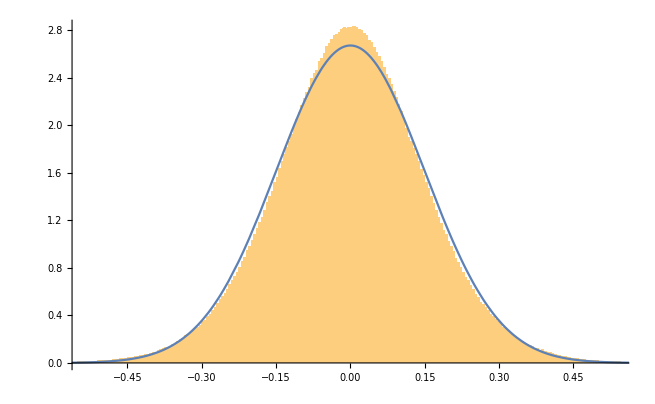

```mathematica
Show[
Histogram[Join[diag, offdiag], 400, PDF],
Plot[With[{σ=σ},1/(√(2π)σ)Exp[-1/(2 σ^2)x^2]], {x, -1, 1}]
]
```

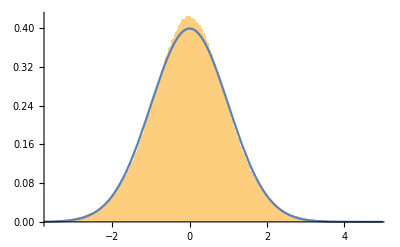

```mathematica
Show[
Histogram[Standardize[Flatten@data[[10000;;, 2;;73]]], 400, PDF],
Plot[With[{σ=1},1/(√(2π)σ)Exp[-1/(2 σ^2)x^2]], {x, -5, 5}]
]
```

```mathematica
e = Table[(If[Mod[tt, 100]==0, Print[tt]]; energy[data[[tt+99000]]]), {tt, 1, 1000}];
```

100

200

300

400

500

600

700

800

900

1000

```mathematica
pot[line_] := Module[{x, n}, (
n = Length[line];
Evaluate[Array[x, $K]] = Partition[line[[2;;(n-1)/2+1]], (($N)^2-1)];

{line[[1]], Sum[1/4 comm[x[i], x[j], $fSU].comm[x[i], x[j], $fSU], {i, 1, $K}, {j, i+1, $K}]}
)];
```

```mathematica
V = Table[(If[Mod[t, 100]==0, Print[t]]; pot[data[[t]]]), {t, 1, 1000}];
```

100

200

300

400

500

600

700

800

900

1000

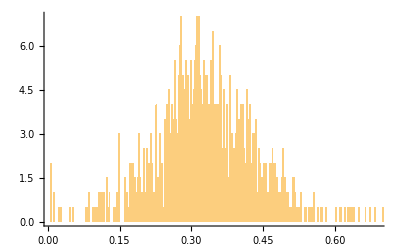

```mathematica
Histogram[V[[All, 2]], 400, PDF]
```

```mathematica
Partition[Range[$K*(($N)^2-1)], (($N)^2-1)]
```

{{1,2,3,4,5,6,7,8},{9,10,11,12,13,14,15,16},{17,18,19,20,21,22,23,24},{25,26,27,28,29,30,31,32},{33,34,35,36,37,38,39,40},{41,42,43,44,45,46,47,48},{49,50,51,52,53,54,55,56},{57,58,59,60,61,62,63,64},{65,66,67,68,69,70,71,72}}

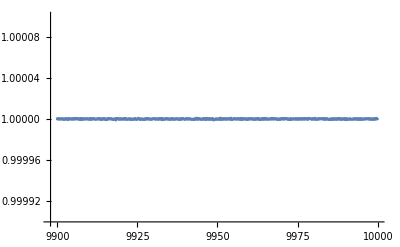

```mathematica
ListPlot[e, PlotRange->{Automatic, {0.9999, 1.0001}}]
```